1/4

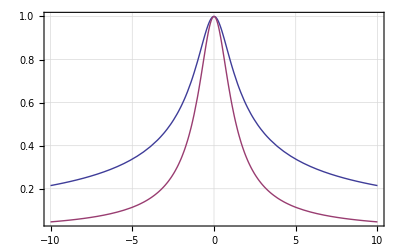

(√π Gamma[1/6])/Gamma[2/3]

```mathematica
Integrate[x^2*Exp[-2*x],{x,0,Infinity}]
psi[x_]:=1/(1+x^2)^(1/3);
plotOptions={PlotRange -> All, GridLines -> Automatic, Frame -> True, PlotStyle -> Thick};
Print[Plot[{psi[x],psi[x]^2},{x,-10,10},Evaluate[plotOptions]]];

Simplify[Integrate[psi[x]^2,{x,-Infinity,Infinity}]]
```